```mathematica
VarMix =ParallelTable[
Var= Table[
n=50;
mu = RandomVariate[NormalDistribution[-15,0.5],n];
sig = Table[x,{n}];(1/n^2)*(Sum[n*sig[[i]]^2 + (n-1)*mu[[i]]^2 - Sum[mu[[i]]*mu[[j]]Boole[i≠j],{j,1,n}],{i,1,n}]),
{rep,1,10000}],
(*{x,Mean[Var]},*)
{x,0.1,2,0.05}];
```

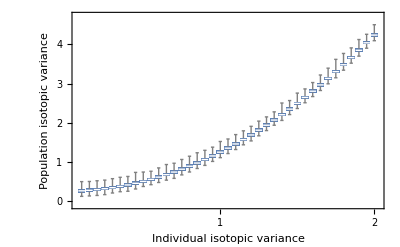

```mathematica
IndPopVarPlot=BoxWhiskerChart[VarMix,ChartStyle->ColorData[97,1],ChartLabels->Table[If[Mod[x+1,IntegerPart[x]+1]==0,IntegerPart[x],""],{x,0.1,2,0.05}],
FrameLabel->{"Individual isotopic variance","Population isotopic variance"}]
```

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2015_DynamicIsotopes/Manuscript/fig_indpopvar.pdf",IndPopVarPlot]
```

/Users/justinyeakel/Dropbox/PostDoc/2015_DynamicIsotopes/Manuscript/fig_indpopvar.pdf

```mathematica
VarMix[[25]][[All,2]]
```

{26.2992,27.2518,26.0412,27.5196,28.5856,32.2519,27.7743,25.7432,9984,27.7593,27.8591,29.4002,28.064,25.9947,29.3954,29.0065,28.3499}
 |  |  |  |

```mathematica
Length[VarMix]
```

25

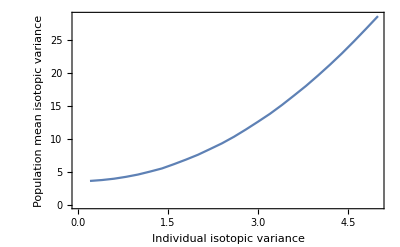

```mathematica
ListPlot[VarMix,Frame->True,FrameLabel->{"Individual isotopic variance","Population mean isotopic variance"},Joined->True]
```

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2015_DynamicIsotopes/Manuscript/fig_indpopvar.pdf",IndPopVarPlot]
```

/Users/justinyeakel/Dropbox/PostDoc/2015_DynamicIsotopes/Manuscript/fig_indpopvar.pdf

```mathematica
Table[If[IntegerQ[x],ToString[x]," "],{x,1,10,0.5}]
```

{ , , , , , , , , , , , , , , , , , , }

```mathematica
ToInt[x_] :=If[IntegerQ[x],ToString[x],""]
```

```mathematica
Table[x,{x,1,10,0.5}]
```

{1.,1.5,2.,2.5,3.,3.5,4.,4.5,5.,5.5,6.,6.5,7.,7.5,8.,8.5,9.,9.5,10.}

```mathematica
ToInt/@Table[x,{x,1,10,0.5}]
```

{,,,,,,,,,,,,,,,,,,}

```mathematica
IntegerQ[1.0]
```

False

```mathematica
Mod[1.5,IntegerPart[1.5]]
```

0.5